Possible implementations of network evolution

```mathematica
vi = {vix,viy,0};
via = {vax,vay,0};
vib = {vbx,vby,0};

A = Sqrt[Cross[via,vi].Cross[via,vi]]+Sqrt[Cross[vi,vib].Cross[vi,vib]]+Sqrt[Cross[vib,via].Cross[vib,via]];
ria = vi - via;
rib = vib - vi;
riba =  Sqrt[rib.rib];
riaa = Sqrt[ria.ria];
P =riaa+riba+Sqrt[(rib+ria).(rib+ria)];
En = K/2*(A-a)^2+G/2*P^2+L*(Sqrt[ria.ria]+Sqrt[rib.rib]);

F = -{D[En,vix],D[En,viy]}/. A -> An/.P -> Pn/.(-vay vix+vax viy)/(√(-vay vix+vax viy)^2)-> 1/. (vby vix-vbx viy)/(√(vby vix-vbx viy)^2)-> 1/.1/(√((vbx-vix)^2+(vby-viy)^2))->1/rbi/.1/(√((-vax+vix)^2+(-vay+viy)^2))-> 1/rai;
F/.(vbx-vix)/rbi-> nibx/.(-vax+vix)/rai->- niax/.(vby-viy)/rbi-> niby/.(-vay+viy)/rai->- niay/.K->0
```

{-L (-niax-nibx)-G (-niax-nibx) Pn,-L (-niay-niby)-G (-niay-niby) Pn}

```mathematica
z = {0,0,1};
nA = Cross[z,via-vib]
```

{-vay+vby,vax-vbx,0}

```mathematica
Endev = En/.vix-> vix+dx/.viy-> viy+dy;
```

Now we will consider a set of coefficients and parameters to get the force acting on a vertex on a square.

```mathematica
vu = {-2.5,2.5,0};
va = {2.5,2.5,0};
vb = {-2.5, -2.5,0};
zunit= {0,0,1};

A = 25;
P = 20;
K = 0.006;
A0 = Pi*(5/3)^2;
G = 1;
L = -1;

nA = Cross[ zunit,va-vb];
rua = vu - va;
rbu = vb-vu;
nua = rua/Sqrt[rua.rua];
nbu = rbu/Sqrt[rbu.rbu];
nP = nua-nbu;

F = -K/2*(A-A0)*nA-(G*P+L/2)*nP
```

{19.7441,-19.7441,0.}

```mathematica
{2.5,2.5,0}
```

{2.5,2.5,0}

Exploring the adjacency and Laplace matrices of a graph undergoing a rearrangement

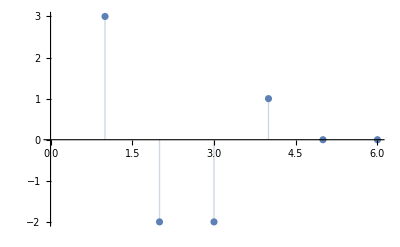

```mathematica
G1 = UndirectedGraph[{1-> 2,1-> 4,1-> 3,2-> 5,2-> 6,4->3,3 -> 6, 6-> 5,5-> 4}];
A1 = AdjacencyMatrix[G1];
Eigenvalues[A1];


G2 = UndirectedGraph[{1-> 2,1-> 4,1-> 5,2-> 3,2-> 6,4->3,3 -> 6, 6-> 5,5-> 4}];
A2 = AdjacencyMatrix[G2];
ListPlot[Eigenvalues[A2],Filling->Axis]
```

This expression is the energy for the minimal wound area after a change of variable a to ar = a^(1/2). It turns this root polynomial into a cubic polynomial that can be more readily solved

```mathematica
dEda[ar_,b_,L_,n_]:= (0.5/(4 Pi) - 0.5/(b*Sqrt[4 Pi])- 0.25/(n*4 Pi)+2/(L*(n-1)*Sqrt[4 Pi]))*ar + (1/(L*(n-1)*Sqrt[4 Pi]) + 0.25/(n*4 Pi))*ar^3 -1
```

30

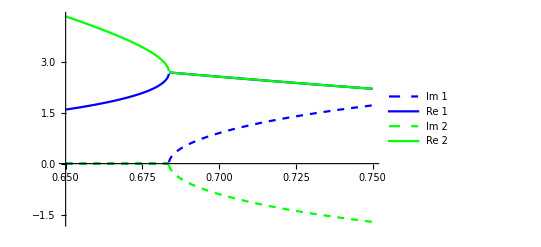

```mathematica
nInput = 30
r = Solve[dEda[a,b,500*b,nInput]== 0,a];
r1 = r[[1]][[1]];
s1 = a/.r1;
ss1 = s1^2;

r2 = r[[2]][[1]];
s2 = a/.r2;
ss2 = s2^2;

r3 = r[[3]][[1]];
s3 = a/.r3;
ss3 = s3^2;


Plot[{Im[ss1/nInput],Re[ss1/nInput],Im[ss2/nInput],Re[ss2/nInput]},{b,0.65,0.75},PlotStyle-> {{Blue,Dashed},Blue,{Green,Dashed},Green,{Red, Dashed},Red}, PlotLegends->{HoldForm["Im 1"],HoldForm["Re 1"],HoldForm["Im 2"],HoldForm["Re 2"],HoldForm["Im 3"],HoldForm["Re 3"]}]
```

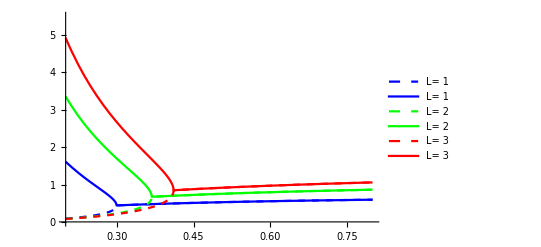

```mathematica
Out[1314]=
```

```mathematica
30
```

30

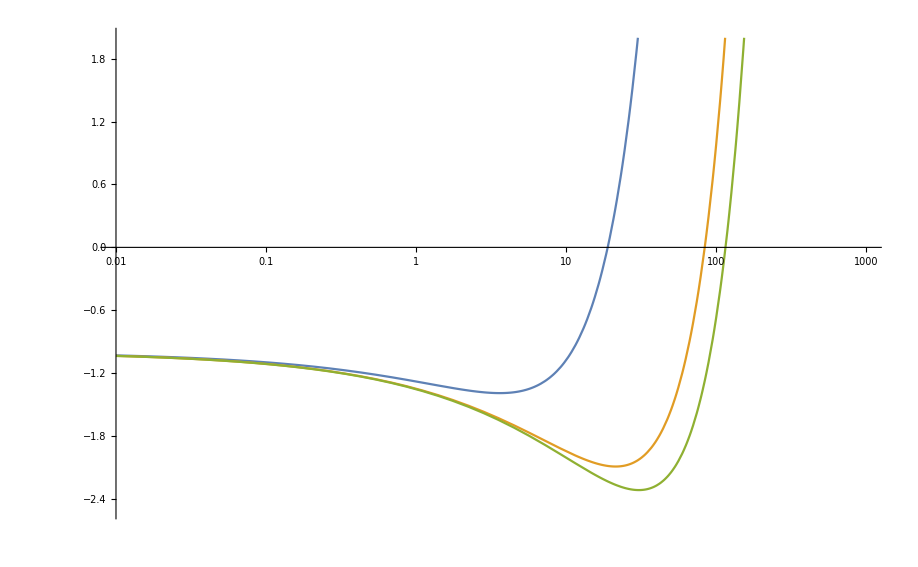

```mathematica
LogLinearPlot[{dEda[ar^(0.5),0.35,0.35,nInput],dEda[ar^(0.5),0.35,2,nInput],dEda[ar^(0.5),0.35,3,nInput]},{ar,0.01,1000},PlotRange->{-2.5,2}]
```

```mathematica
b
```

```mathematica
ss3
```

(-((41.9392 (-9.05775×10^26+2.29707×10^26 b+1.98695×10^25 b^2))/((8.01011×10^9+5.46073×10^8 b) (7.57901×10^55 b+1.03337×10^55 b^2+3.52238×10^53 b^3+√(2.11634×10^29 (-9.05775×10^26+2.29707×10^26 b+1.98695×10^25 b^2)^3+(7.57901×10^55 b+1.03337×10^55 b^2+3.52238×10^53 b^3)^2))^(1/3)))+1/(8.01011×10^9+5.46073×10^8 b)7.03761×10^-9 (7.57901×10^55 b+1.03337×10^55 b^2+3.52238×10^53 b^3+√(2.11634×10^29 (-9.05775×10^26+2.29707×10^26 b+1.98695×10^25 b^2)^3+(7.57901×10^55 b+1.03337×10^55 b^2+3.52238×10^53 b^3)^2))^(1/3))^2

```mathematica
}
```